## Analysis of output from PACT

Copyright 2009-2010 Trevor Bedford

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Dropbox/current-projects/sismid/phylogenetics/practical/pact

## Setup

```mathematica
colorlist={RGBColor[0.857,0.131,0.132],RGBColor[0.324,0.609,0.708],RGBColor[0.765,0.728,0.274],RGBColor[0.513,0.73,0.442],RGBColor[0.394,0.113,0.593],RGBColor[0.6,0.4,0.2],RGBColor[0.251,0.225,0.769],RGBColor[0.902,0.541,0.209]};
```

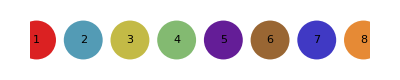

```mathematica
Graphics[MapIndexed[{PointSize[0.07],#1,Point[{First@#2,0}],Black,Text[First@#2,{First@#2,0}]}&,colorlist],ImageSize->400,AspectRatio->0.2]
```

```mathematica
n=8;
```

```mathematica
names={"c1","c2","c3","c4","c5","c6","c7","c8"};
```

```mathematica
colorrules=MapThread[#1->#2&,{names,colorlist}]
```

{c1→RGBColor[0.857, 0.131, 0.132],c2→RGBColor[0.324, 0.609, 0.708],c3→RGBColor[0.765, 0.728, 0.274],c4→RGBColor[0.513, 0.73, 0.442],c5→RGBColor[0.394, 0.113, 0.593],c6→RGBColor[0.6, 0.4, 0.2],c7→RGBColor[0.251, 0.225, 0.769],c8→RGBColor[0.902, 0.541, 0.209]}

## Vaccine strains

```mathematica
vaccineStrains={
"A/Johannesburg/33/1994",
"A/Wuhan/359/1995",
"A/Sydney/5/1997",
"A/Moscow/10/1999",
"A/Fujian/411/2002",
"A/California/7/2004",
"A/Wisconsin/67/2005",
"A/Brisbane/10/2007",
"A/Perth/16/2009",
"A/Victoria/361/2011",
"A/Texas/50/2012"
};
```

## Tree

```mathematica
{tips,trunk,rules,labels,coords,ids,antigenic}=Import["out.rules","Table"];
```

```mathematica
rules=ToExpression[rules];coords=ToExpression[coords];
```

```mathematica
labels=Map[With[{split=StringSplit[#,"->"]},ToExpression[split[[1]]]->split[[2]]]&,labels];
```

```mathematica
ids=Map[With[{split=StringSplit[#,"->"]},ToExpression[split[[1]]]->First[StringSplit[split[[2]],"|"]]]&,ids];
```

```mathematica
branchLines=Map[{#[[1]]/.labels/.colorrules,With[{coordsA=#[[1]]/.coords,coordsB=#[[2]]/.coords},Line[{coordsA,{coordsB[[1]],coordsA[[2]]},coordsB}]]}&,rules];
```

```mathematica
tipCircles={PointSize[0.005],Map[{#/.labels/.colorrules,Point[(#/.coords)]}&,tips]};
```

```mathematica
vaccineLabels={Directive[Black,FontFamily->"Helvetica",FontSize->8],DeleteCases[Map[If[MemberQ[vaccineStrains,#/.ids],{#/.labels/.colorrules,Text[#/.ids,(#/.coords)+{2.25,0},{-1,0}]},Null]&,tips],Null]};
```

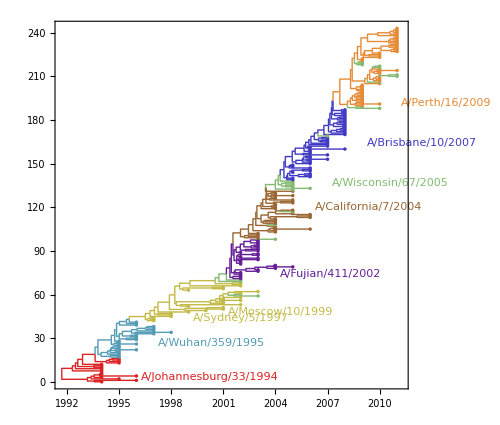

```mathematica
fig=Graphics[{branchLines,tipCircles,vaccineLabels},ImageSize->500,AspectRatio->0.85,Frame->{True,False,False,False},FrameStyle->Directive[FontSize->9,Black,FontFamily->"Helvetica"]]
```

```mathematica
Export["vaccine_tree.png",fig,"PNG",ImageResolution->180]
```

vaccine_tree.png